```mathematica
Shapes 2 - Nathan Yee
```

2 Shapes-Nathan Yee

```mathematica
Question 1
```

```mathematica
makeGrid[names_,equations_,graphs_] := Grid[Transpose[{Table[TraditionalForm[i],{i,names}],Table[TraditionalForm[i],{i,equations}],Table[TraditionalForm[i],{i,graphs}]}],Frame->All]
```

```mathematica
equations1 = {x^n, Sin[x],Cos[x],ⅇ^x,Log[x],Tan[x]};
```

```mathematica
derivatives1 = D[equations1,x]
```

{n x^(-1+n),Cos[x],-Sin[x],ⅇ^x,1/x,Sec[x]^2}

```mathematica
integrals1 = Integrate[equations1,x];
```

```mathematica
grid1=makeGrid[equations1,derivatives1,integrals1]
```

x^n | n x^(n-1) | x^(n+1)/(n+1)
sin(x) | cos(x) | -cos(x)
cos(x) | -sin(x) | sin(x)
ⅇ^x | ⅇ^x | ⅇ^x
log(x) | 1/x | x log(x)-x
tan(x) | sec^2(x) | -log(cos(x))

```mathematica
grid1=ReplacePart[grid1,1->Prepend[First[grid1],{"Equation","Derivative","Integral"}]]
```

Equation | Derivative | Integral
x^n | n x^(n-1) | x^(n+1)/(n+1)
sin(x) | cos(x) | -cos(x)
cos(x) | -sin(x) | sin(x)
ⅇ^x | ⅇ^x | ⅇ^x
log(x) | 1/x | x log(x)-x
tan(x) | sec^2(x) | -log(cos(x))

```mathematica
grid1=Insert[grid1,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->All,Spacings->{2,{2,{0.7},2}}},2]
```

Equation | Derivative | Integral
x^n | n x^(n-1) | x^(n+1)/(n+1)
sin(x) | cos(x) | -cos(x)
cos(x) | -sin(x) | sin(x)
ⅇ^x | ⅇ^x | ⅇ^x
log(x) | 1/x | x log(x)-x
tan(x) | sec^2(x) | -log(cos(x))

```mathematica
Question 4
```

```mathematica
Rasterize[Grid[{{"Equation","Derivative"},{(x^3-1)^100,D[(x^3-1)^100,x]}},Frame->All]]
```

-Graphics-

```mathematica
Question 5
```

```mathematica
Rasterize[Grid[Transpose[{{"∫_0^4 Sqrt[2x+1]ⅆx"},{Integrate[Sqrt[2x+1],{x,0,4}]}}],Frame->All]]
```

-Graphics-

```mathematica
Question 6
```

```mathematica
Rasterize[Grid[{{"Equation","Derivative"},{√x(1-x),D[√x(1-x),x]}},Frame->All]]
```

-Graphics-

```mathematica
Question 7
```

```mathematica
Rasterize[Grid[{{"Equation","Integral"},{TraditionalForm["∫_2^1 xⅇ^-xⅆx"],TraditionalForm[∫_2^1 xⅇ^-x ⅆx]}},Frame->All]]
```

-Graphics-

```mathematica
Question 8
```

```mathematica
Rasterize[Grid[{{"Equation","Integral"},{TraditionalForm["∫_(.825)^0 x^20ⅆx"],TraditionalForm[∫_(.825)^0 x^20 ⅆx]}},Frame->All]]
```

-Graphics-

```mathematica
Question 9
```

```mathematica
SetDirectory[NotebookDirectory[]];
<< ToMatlab.m
MyToMatlab[x_] := ToMatlab[x]
```

```mathematica
Clear[x]
Clear[d]
Clear[n]
```

```mathematica
Integrate[d-x^n,{x,0,d^(1/n)}]
```

ConditionalExpression[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n),Re[n]>-1]

```mathematica
ConditionalExpression[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n),Re[n]>-1]
```

ConditionalExpression[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n),Re[n]>-1]

```mathematica
ToMatlab[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n)]
```

d.^(1+n.^(-1))+(-1).*(d.^(n.^(-1))).^(1+n).*(1+n).^(-1);

```mathematica
n=3
```

3

```mathematica
LogLogPlot[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n),{d,0,100}]
```

LogLogPlot::llplim: Range specification LogLogPlot is not of the form {x, xmin, xmax} with xmin and xmax positive.

LogLogPlot[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n),{d,0,100}]

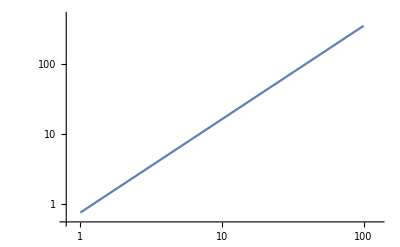

```mathematica
LogLogPlot[d^(1+1/n)-((d^(1/n))^(1+n))/(1+n),{d,1,100}]
```

```mathematica
Show[%1262,AxesLabel->{HoldForm[d ],HoldForm[Integration]},PlotLabel->HoldForm[n=3],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Out is not a type of graphics.

Show[%1262,AxesLabel→{d,Integration},PlotLabel→(n=3),LabelStyle→{GrayLevel[0]}]

```mathematica
Question 10
```

```mathematica
Clear[y]
```

```mathematica
equations10=x^2*Sin[x*y^2]
```

x^2 Sin[x y^2]

```mathematica
partial10x=D[equations10,x]
```

x^2 y^2 Cos[x y^2]+2 x Sin[x y^2]

```mathematica
partial10y=D[equations10,y]
```

2 x^3 y Cos[x y^2]

```mathematica
2 x^3 y Cos[x y^2]
```

2 x^3 y Cos[x y^2]

```mathematica
list10={TraditionalForm[equations10],TraditionalForm[partial10x],TraditionalForm[partial10y]}
```

{x^2 sin(x y^2),x^2 y^2 cos(x y^2)+2 x sin(x y^2),2 x^3 y cos(x y^2)}

```mathematica
names10={"Equation","Partial x","Partial y"}
```

{Equation,Partial x,Partial y}

```mathematica
Rasterize[Grid[{names10,list10},Frame->All]]
```

-Graphics-

```mathematica
Question 11
```

```mathematica
equations11=x^2*Sin[x*y^2]
```

x^2 Sin[x y^2]

```mathematica
partial10xx=D[equations10,x,x]
```

4 x y^2 Cos[x y^2]+2 Sin[x y^2]-x^2 y^4 Sin[x y^2]

```mathematica
partial10xy=D[equations10,x,y]
```

6 x^2 y Cos[x y^2]-2 x^3 y^3 Sin[x y^2]

```mathematica
partial10yx=D[equations10,y,x]
```

6 x^2 y Cos[x y^2]-2 x^3 y^3 Sin[x y^2]

```mathematica
partial10yy=D[equations10,y,y]
```

2 x^3 Cos[x y^2]-4 x^4 y^2 Sin[x y^2]

```mathematica
list11={TraditionalForm[equations11],TraditionalForm[partial10xx],TraditionalForm[partial10xy],TraditionalForm[partial10xy],TraditionalForm[partial10yy]}
```

{x^2 sin(x y^2),-x^2 y^4 sin(x y^2)+2 sin(x y^2)+4 x y^2 cos(x y^2),6 x^2 y cos(x y^2)-2 x^3 y^3 sin(x y^2),6 x^2 y cos(x y^2)-2 x^3 y^3 sin(x y^2),2 x^3 cos(x y^2)-4 x^4 y^2 sin(x y^2)}

```mathematica
names11={"Equation","Partial xx","Partial xy","Partial yx","Partial yy"}
```

{Equation,Partial xx,Partial xy,Partial yx,Partial yy}

```mathematica
Rasterize[Grid[Transpose[{names11,list11}],Frame->All]]
```

-Graphics-

```mathematica
Question 14
```

```mathematica
list14={x,Sin[x],Log[x]}
```

{x,Sin[x],Log[x]}

```mathematica
plots14 = {}
```

{}

```mathematica
PlotFunction14[z_,a_,b_]:=AppendTo[plots14,Plot[z,{x,a,b},Filling->Axis]]
```

```mathematica
PlotFunction[list14[[1]],0,1];
```

```mathematica
PlotFunction14[list14[[2]],0,Pi/2];
```

```mathematica
PlotFunction14[list14[[3]],1,2];
```

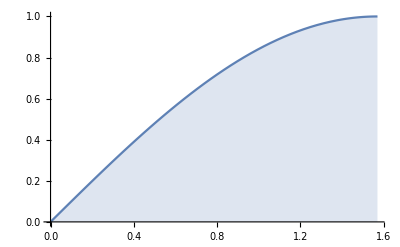
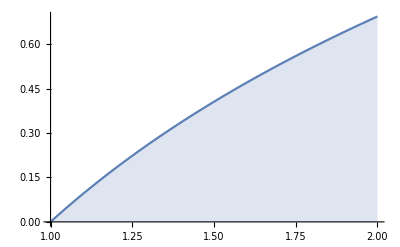

```mathematica
plots14
```

```mathematica
integrals14={Integrate[list14[[1]],{x,0,1}],Integrate[list14[[2]],{x,0,4}],Integrate[list14[[3]],{x,1,2}]}
```

{1/2,2 Sin[2]^2,-1+Log[4]}

```mathematica
grid14=Grid[Transpose[{list14,plots14,integrals14}],Frame->All];
```

Transpose::nmtx: The first two levels of … cannot be transposed.

```mathematica
grid14=ReplacePart[grid14,1->Prepend[First[grid14],{"First Integration","Sketch","Second Integration"}]]
```

Transpose::tperm: Permutation … is longer than the dimensions {3} of the expression.

Grid[Transpose[{First Integration,Sketch,Second Integration},{{x,Sin[x],Log[x]},{-Graphics-,-Graphics-},{1/2,2 Sin[2]^2,-1+Log[4]}}],Frame→All]

```mathematica
Rasterize[Insert[grid14,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]]
```

Transpose::tperm: Permutation … is longer than the dimensions {3} of the expression.

-Graphics-

```mathematica
Question 15
```

```mathematica
Question 15
```

```mathematica
ClearAll[list15,plots15,integrals15,PlotFunction15]
```

```mathematica
list15={Integrate[1,{y,y,2-y}],Integrate[1,{y,y/2,2}],Integrate[1,{y,y,Log[y]}]}
```

{2-2 y,2-y/2,-y+Log[y]}

```mathematica
{2-2 y,2-y/2,-y+Log[y]}
```

{2-2 y,2-y/2,-y+Log[y]}

```mathematica
plots15 = {}
```

{}

```mathematica
PlotFunction15[z_,a_,b_]:=AppendTo[plots15,Plot[z,{y,a,b},Filling->Axis]]
```

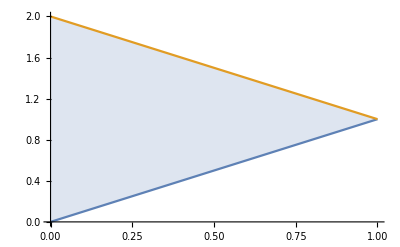
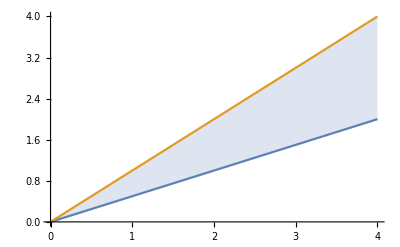
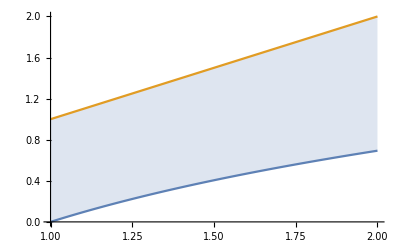

```mathematica
plots15={Plot[{y,2-y},{y,0,1},Filling->{1->{2}}],Plot[{y/2,y},{y,0,4},Filling->{1->{2}}],Plot[{Log[y],y},{y,1,2},Filling->{1->{2}}]}
```

```mathematica
integrals15={Integrate[list15[[1]],{y,0,1}],Integrate[list15[[2]],{y,0,4}],Integrate[list15[[3]],{y,1,2}]}
```

{1,4,-5/2+Log[4]}

```mathematica
grid15=Grid[Transpose[{plots15,list15,integrals15}],Frame->All]
```

-Graphics- | 2-2 y | 1
-Graphics- | 2-y/2 | 4
-Graphics- | -y+Log[y] | -5/2+Log[4]

```mathematica
grid15=ReplacePart[grid15,1->Prepend[First[grid15],{"Sketch","First Integration","Second Integration"}]]
```

Sketch | First Integration | Second Integration
-Graphics- | 2-2 y | 1
-Graphics- | 2-y/2 | 4
-Graphics- | -y+Log[y] | -5/2+Log[4]

```mathematica
grid15=Rasterize[Insert[grid15,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]]
```

-Graphics-

```mathematica
Question 16
```

```mathematica
Integrate[1+x^2,{x,0,2}]-Integrate[y^2,{y,-1,1}] - Integrate[-1,{x,-1,1}]
```

6

```mathematica
Question 17
```

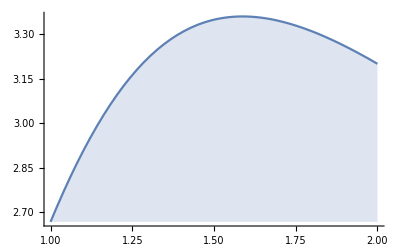

```mathematica
slice17=Plot[Integrate[(4y)/(x^3+2),{y,0,2*x}],{x,1,2},Filling->Bottom]
```

```mathematica
slice17=Show[plot17,AxesLabel->{HoldForm[x],None},PlotLabel->HoldForm[Slice at z=0],LabelStyle->{GrayLevel[0]}]
```

Show::gtype: Symbol is not a type of graphics.

Show[plot17,AxesLabel→{x,None},PlotLabel→(Slice at z=0),LabelStyle→{GrayLevel[0]}]

```mathematica
TraditionalForm[Integrate[(4y)/(x^3+2),{x,1,2},{y,0,2*x}]]
```

8/3 log(10/3)

```mathematica
.14Integrate[(4y)/(x^3+2),{y,0,2*x},{x,1,2}]
```

.14Integrate[(4 y)/(2+x^3),{y,0,2 x},{x,1,2}]

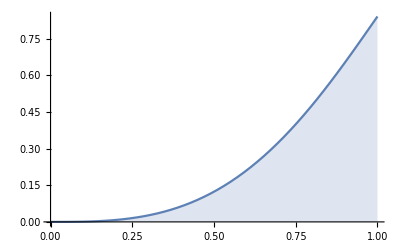

```mathematica
slice17b = Plot[Integrate[x*Cos[y],{y,0,x^2}],{x,0,1},Filling->Bottom]
```

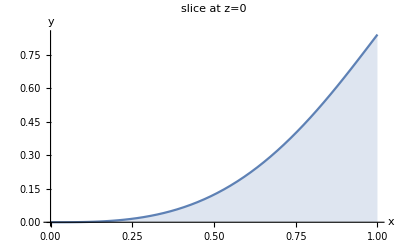

```mathematica
slice17=Show[slice17b,AxesLabel->{HoldForm[x],HoldForm[y]},PlotLabel->HoldForm[slice at z=0],LabelStyle->{GrayLevel[0]}]
```

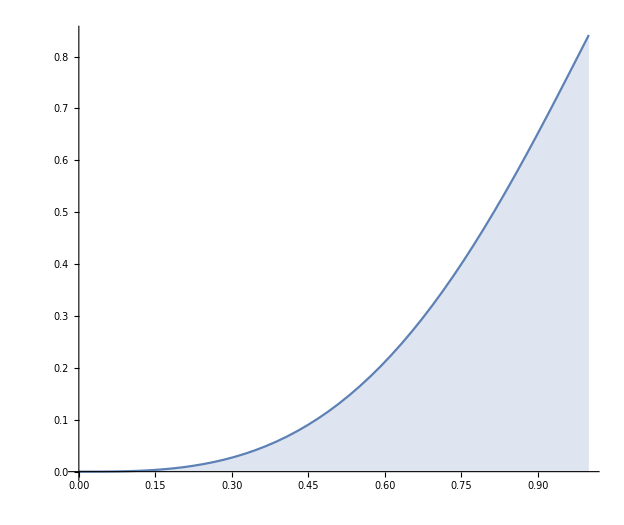

```mathematica
slice17=Show[slice17b,ImageSize->{624,Automatic},AspectRatio->Full]
```

```mathematica
TraditionalForm[Integrate[x*Cos[y],{x,0,1},{y,0,x^2}]]
```

sin^2(1/2)

```mathematica
Question 18
```

```mathematica
Clear[y]
Clear[z]
```

```mathematica
slice18a=ContourPlot3D[x+y+z==1,{x,0,1},{y,0,1},{z,0,1}]
```

-Graphics3D-

```mathematica
Integrate[1-x-y,{y,0,1},{x,0,1-y}]
```

1/6

```mathematica
RegionPlot3D[z<x^2+y^2&&y>x^2&&x>y^2,{x,0,1},{y,0,1},{z,0,2}]
```

-Graphics3D-

```mathematica
RegionPlot3D[z<x^2+y^2&&y>x^2&&x>y^2,{x,0,1},{y,0,1},{z,0,2},Mesh->Automatic,MeshFunctions->{#3&}]
```

-Graphics3D-

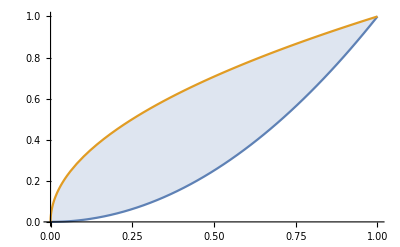

```mathematica
Plot[{y^2,Sqrt[y]},{y,0,1},Filling->{1->{2}}]
```

```mathematica
Integrate[x^2+y^2,{x,0,1},{y,x^2,x^(1/2)}]
```

6/35

```mathematica
Question 11
```

```mathematica
Question 11
```

```mathematica
Question 11
```

```mathematica
Question 11
```

```mathematica
Integrate[2*x*y*z,{x,0,1},{y,x,2x},{z,0,y}]
```

5/8